# Backbending in nuclei

```mathematica
energies162=Sort[{4463.2,3846.6,3292.4,2745.72,2165.12,1602.83,1096.70,666.68,329.62,102.04,0}];
spins162=Table[i,{i,0,20,2}];
energiesYb160=Sort[{14200.6,13042.6,11964.6,10957.6,10003.6,9126.6,8289.6,7458.9,6623.2,5827.6,5091.2,4427.50,3849.10,3365.00,2960.80,2374.32,1736.79,1147.16,638.39,243.00,0.0}];
spinsYb160=Table[i,{i,0,40,2}];
```

## MOIS and Rotational Frequencies

```mathematica
mois[energies_,spins_]:=Table[(4*spins[[i]]-2)/((energies[[i]]-energies[[i-1]])/1000),{i,2,Length[energies]}];
hrots[energies_,spins_]:=Table[Sqrt[4*(spins[[i]]^2-spins[[i]]+1)*(((energies[[i]]-energies[[i-1]])/1000)/(4*spins[[i]]-2))^2],{i,2,Length[energies]}];
hrotsBertulani[energies_,spins_]:=Table[((energies[[i]]-energies[[i-1]])/1000)/2,{i,2,Length[energies]}];
hrotsSquared[energies_,spins_]:=#^2&/@hrots[energies,spins];
```

## Plots

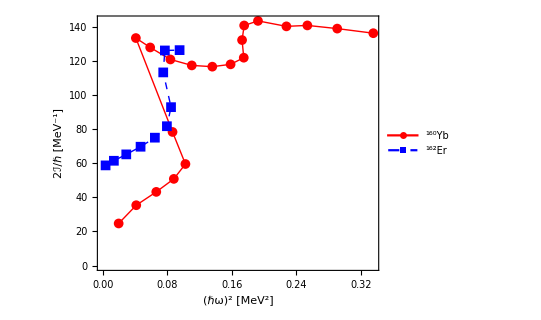

```mathematica
nucleus[name_,a_]:=Row[{Superscript["",a],name}];Er162Data=Table[{hrotsSquared[energies162,spins162][[i]],mois[energies162,spins162][[i]]},{i,1,Length[mois[energies162,spins162]]}];
Yb160Data=Table[{hrotsSquared[energiesYb160,spinsYb160][[i]],mois[energiesYb160,spinsYb160][[i]]},{i,1,Length[mois[energiesYb160,spinsYb160]]}];
ListPlot[{Yb160Data,Er162Data},Joined->True,Joined->True,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],AspectRatio->0.8,PlotRange->Full,Joined->True,PlotMarkers->{Automatic, Medium},PlotStyle->{{Red,Thick},{Blue,Dashed,Thick}},PlotLegends->Placed[{nucleus["Yb","160"],nucleus["Er","162"]},Scaled[{0.76,0.3}]],LabelStyle->{18,Bold,Black,FontFamily->"Times"},FrameLabel->{"(ℏω)^2 [MeV^2]","2ℐ/ℏ [MeV^-1]"},ImageSize->400]
```